# Analysis of Packing V3E05L0N01T1_1

Three Vertices, Five Edges, 0 Loops,Combinatorial Number 01, Face Pattern 1, Type 1

-Graphics-

Assume that one lift of the big circle, circle 1, is at the origin. Let α be the angle at the apex of isosceles triangle (0,0), Circle 2, lift of circle1 the is horizontal from the origin via vector w1. Let β be the angle at the apex of isosceles triangle (0,0), Circle 3, lift of circle (via vector w2). This means that the center of circle 2 is

 ((rs+rb)*Cos[Pi/2-α/2], (rs+rb)*Sin[Pi/2-α/2]) = (Sqrt[2]rb*Cos[Pi/2-α/2], Sqrt[2]rb*Sin[Pi/2-α/2]) 

The law of cosines on the isosceles triangle containing α implies that the square of the length of the ‘horizontal’ vector is (note rs+rb = Sqrt[2]rb)

(Sqrt[2]rb)^2 + (Sqrt[2]rb)^2 - 2*(Sqrt[2]rb)(Sqrt[2]rb)Cos[α] = 4rb^2 - 4rb^2Cos[α] = 4rb^2(1-Cos[α]) = (2Sqrt[2]rbSin[α/2])^2

This the vector w1 has coordinates

( 2*Sqrt[2]*rb*Sin[α/2] ,0)

Notice that triangle with vertices at (0,0) and the centers of circles 2 and 3 is isosceles with equal sides of length rs+rb = Sqrt[2]rb and other side of length 2*rs = 2(Sqrt[2]-1)*rb, this means that the angle opposite the non-equal side, γ, satisfies 

(2(Sqrt[2]-1)*rb)^2 == (Sqrt[2]rb)^2 + (Sqrt[2]rb)^2 - 2*(Sqrt[2]rb)(Sqrt[2]rb)^2Cos[γ]

dividing by rb^2 and solving for γ yields

```mathematica
Solve[(2(Sqrt[2]-1))^2 == (Sqrt[2])^2 + (Sqrt[2])^2 - 2*(Sqrt[2])(Sqrt[2])Cos[γ],γ]
N[%]
```

{{γ→ConditionalExpression[-ArcCos[2 (-1+√2)]+2 π C[1],C[1]∈ℤ]},{γ→ConditionalExpression[ArcCos[2 (-1+√2)]+2 π C[1],C[1]∈ℤ]}}

{{γ→ConditionalExpression[-0.594503+6.28319 C[1],C[1]∈ℤ]},{γ→ConditionalExpression[0.594503+6.28319 C[1],C[1]∈ℤ]}}

```mathematica
{{γ->ConditionalExpression[-0.5945027226424133+6.283185307179586 C[1],C[1]∈Integers]},{γ->ConditionalExpression[0.5945027226424133+6.283185307179586 C[1],C[1]∈Integers]}}
```

{{γ→ConditionalExpression[-0.594503+6.28319 C[1],C[1]∈ℤ]},{γ→ConditionalExpression[0.594503+6.28319 C[1],C[1]∈ℤ]}}

```mathematica
N[ArcCos[2 (-1+√2)]]*180/Pi
```

34.0625

Notice that ArcCos[2(-1+√2)] yields an angle of 0.594503 ~ 34.0625 degrees

Therefore circle 3 is centered at 

 ((rs+rb)*Cos[Pi/2-α/2+ArcCos[2 (-1+√2)]], (rs+rb)*Sin[Pi/2-α/2+ArcCos[2 (-1+√2)]]) = (Sqrt[2]rb*Cos[Pi/2-α/2+ArcCos[2(-1+√2)]], Sqrt[2]rb*Sin[Pi/2-α/2+ArcCos[2 (-1+√2)]])
 
 This choice ensures that circles 2 and 3 are tangent.
 
 Using a similar analysis on the triangle containing α, the isosceles triangle containing β has a non-equal length of 2*Sqrt[2]*rb*Sin[β/2], therefore the coordinates of w2 are
 
 (2*Sqrt[2]*rb*Sin[β/2] Cos[Pi/2-α/2+ArcCos[2 (-1+√2)]+Pi-β/2], 2*Sqrt[2]*rb*Sin[β/2]*Sin[[Pi/2-α/2+ArcCos[2 (-1+√2)]+Pi-β/2])

Note that the whole picture scales, so we can choose a scale factor so that rb =1/2.  This is the same as scaling the picture so that one vector has length 1.

## Circle Centers and Radii

```mathematica
centers = {{0,0},
{Sqrt[2]/2Cos[Pi/2-α/2],
Sqrt[2]/2Sin[Pi/2-α/2]},
{Sqrt[2]/2Cos[Pi/2-α/2+ArcCos[2(-1+√2)]],
Sqrt[2]/2Sin[Pi/2-α/2+ArcCos[2 (-1+√2)]]}}
```

{{0,0},{Sin[α/2]/(√2),Cos[α/2]/(√2)},{Sin[α/2-ArcCos[2 (-1+√2)]]/(√2),Cos[α/2-ArcCos[2 (-1+√2)]]/(√2)}}

## Lattice Vectors

We are working this flat torus

```mathematica
latticeVectors = {
 {2*Sqrt[2]/2*Sin[α/2],0},
{ 2*Sqrt[2]/2*Sin[β/2]*Cos[Pi/2-α/2+ArcCos[2 (-1+√2)]+Pi/2-β/2],2*Sqrt[2]/2*Sin[β/2]*Sin[Pi/2-α/2+ArcCos[2 (-1+√2)]+Pi/2-β/2]}};
```

## Edges

Here we store the edges a list {i,j,m,n} where center[[i]] is connected to center[[j]] + m*latticeVectors[[1]] + n*latticeVectors[2]]
center[[i]] is *always* in the fundamental domain ****the last two numbers are winding numbers****

```mathematica
edges = {{1,2,0,0},{1,3,0,0},{2,3,0,0},{3,1,0,1},{2,1,1,0}};
```

### Check the edge lengths are all 2rs= Sqrt[2]-1 or rs+rb=Sqrt[2]rb=Sqrt[2]/2=1/Sqrt[2]

```mathematica
For[i=1,i≤Length[edges],i++,Print["Edge ",i,": Length is ",FullSimplify[
EuclideanDistance[centers[[edges[[i,1]] ]],centers[[edges[[i,2]] ]]+
edges[[i,3]]*latticeVectors[[1]]+
edges[[i,4]]*latticeVectors[[2]]],{rb>0,α<Pi,β<Pi,Pi/2+ArcCos[2 (-1+√2)]/2<α,Pi/2+ArcCos[2 (-1+√2)]/2<β}]]]
```

Edge 1: Length is 1/(√2)

Edge 2: Length is 1/(√2)

Edge 3: Length is -1+√2

Edge 4: Length is 1/(√2)

Edge 5: Length is 1/(√2)

Note that the upper bounds on α and β are Pi, because if either of these angles are bigger than Pi, the circle at 2 (or 3) will have its tangencies restricted to a half circle.  The lower bound of Pi/2+ArcCos[√2 (-1+√2)]/2 comes from the fact that if either of these angle is less than this amount the circles will again have its tangencies restricted to a half circle (that would make the packing not Locally maximally dense.

Notice that edges 1, 2, 4, and 5 are all Sqrt[2]rb = rb+rs,  Edge 3 is 2(Sqrt[2]-1)rb = 2*rs

Yes!

## Packing Visualization

Here we visualize the packing and the fundamental domain to help determine the value of the parameters for which this is a packing graph.

```mathematica
Animate[
Graphics[
Translate[
Union[
Table[{Thick,Dashing[1],Black,Line[{centers[[edges[[i,1]] ]],centers[[edges[[i,2]] ]]+
edges[[i,3]]*latticeVectors[[1]]+
edges[[i,4]]*latticeVectors[[2]]}/.{α->a,β->b}]},{i,1,Length[edges]}],(*Edges*)
{{Thick,Dashed,Blue,Arrow[{{0,0},latticeVectors[[1]]/.{α->a,β->b} }]},{Thick,Dashed,Blue,Arrow[{{0,0},latticeVectors[[2]]/.{α->a,β->b}}]}},(*Fundamental Domain*)
{{AbsolutePointSize[5],Point[centers/.{α->a,β->b}]}},(*Circle Centers*)
Table[Text[Style[i,Medium],centers[[i]]/.{α->a,β->b},Offset[{10,-30},{0,0}]],{i,1,Length[centers]}],(*Label Circle Centers*)
{{Opacity[.5],EdgeForm[Thick],LightOrange,Disk[centers[[1]]/.{α->a,β->b},1/2]},
{Opacity[.5],EdgeForm[Thick],LightGreen,Disk[centers[[2]]/.{α->a,β->b},1/2*(Sqrt[2]-1)]},
{Opacity[.5],EdgeForm[Thick],LightRed,Disk[centers[[3]]/.{α->a,β->b},1/2*(Sqrt[2]-1)]}}, (*Circles*){{Text[Style["α",Small],centers[[2]]/.{α->a,β->b},Offset[{0,10},{0,0}]]},
{Text[Style["β",Small],centers[[3]]/.{α->a,β->b},Offset[{10,-10},{0,0}]]}}(*Angle Markers Labels*)

], Flatten[Table[i*latticeVectors[[1]]+j*latticeVectors[[2]],{i,-2,2,1},{j,-2,2,1}]/.{α->a,β->b},1] (*List of the translation vectors*)
],PlotRange-> {{-1,3},{-1,3}} (*Restrict the plot window*)
],{{a,5Pi/6,"α"},Pi/2+ArcCos[2 (-1+√2)]/2,Pi},{{b,5Pi/6,"β"},0,2Pi},AnimationRunning -> False
]
```

## Locally Maximally Dense

We have to determine for which values of α and β the packing is locally maximally dense. To be locally maximally dense (Following Connelly, Rigid Circle and Sphere Packings, Page 51, Theorem 6.1)
	1. The packing graph is rigid as a bar framework
	2. Have a proper stress that is non-zero on every member

### Rigid as bar framework

To be rigid as a bar framework we need to establish a rigid ordering of the circles. The numbering of the circles in the picture above is a rigid ordering of the packing disks -- See Lemma 6.2 in the Connelly paper on Rigid Sphere and Circle Packings. Note: The first is held fixed.

### Proper Stress

Assign a scalar to each edge of the packing and collect those scalars in a vector called ω. We need to solve the linear algebra problem where the sum of the ω_i times the vector from vertex j is zero.

```mathematica
Animate[
Graphics[
Translate[
Union[
Table[{Thick,Dashing[1],Black,Line[{centers[[edges[[i,1]] ]],centers[[edges[[i,2]] ]]+
edges[[i,3]]*latticeVectors[[1]]+
edges[[i,4]]*latticeVectors[[2]]}/.{α->a,β->b}]},{i,1,Length[edges]}],(*Edges*)
{{Thick,Dashed,Blue,Arrow[{{0,0},latticeVectors[[1]]/.{α->a,β->b} }]},{Thick,Dashed,Blue,Arrow[{{0,0},latticeVectors[[2]]/.{α->a,β->b}}]}},(*Fundamental Domain*)
{{AbsolutePointSize[5],Point[centers/.{α->a,β->b}]}},(*Circle Centers*)
Table[Text[Style[i,Medium],centers[[i]]/.{α->a,β->b},Offset[{10,-30},{0,0}]],{i,1,Length[centers]}],(*Label Circle Centers*)
{{Opacity[.5],EdgeForm[Thick],LightOrange,Disk[centers[[1]]/.{α->a,β->b},1/2]},
{Opacity[.5],EdgeForm[Thick],LightGreen,Disk[centers[[2]]/.{α->a,β->b},1/2*(Sqrt[2]-1)]},
{Opacity[.5],EdgeForm[Thick],LightRed,Disk[centers[[3]]/.{α->a,β->b},1/2*(Sqrt[2]-1)]}}, (*Circles*){{Text[Style["α",Small],centers[[2]]/.{α->a,β->b},Offset[{0,10},{0,0}]]},
{Text[Style["β",Small],centers[[3]]/.{α->a,β->b},Offset[{10,-10},{0,0}]]}},(*Angle Markers Labels*)
Table[Text[Style[Subscript["ω",i],Large,Red],1/2*(centers[[edges[[i,1]] ]]+centers[[edges[[i,2]] ]]+
edges[[i,3]]*latticeVectors[[1]]+
edges[[i,4]]*latticeVectors[[2]])/.{α->a,β->b}],{i,1,Length[edges]}](*Label Edges With Stresses*)

], Flatten[Table[i*latticeVectors[[1]]+j*latticeVectors[[2]],{i,-2,2,1},{j,-2,2,1}]/.{α->a,β->b},1] (*List of the translation vectors*)
],PlotRange-> {{-1,3},{-1,3}} (*Restrict the plot window*)
],{{a,5Pi/6,"α"},Pi/2+ArcCos[2 (-1+√2)]/2,Pi},{{b,5Pi/6,"β"},Pi/2+ArcCos[2 (-1+√2)]/2,Pi},AnimationRunning -> False
]
```

```mathematica
equations = Table[{0,0},{k,Length[centers]}]; (*Start with the zero equations*)
w =Table[Subscript[ω,i],{i,Length[edges]}]; (*Initialize a vector of Subscript[ω, i]*)
For[i=1,i≤Length[centers], i++, (*i is the center number*)
For[j=1,j≤Length[edges], j++, (*j is the edge number*)
If[edges[[j,1]]==i, (*center i is the starting point of edge j*)
equations[[i]] = equations[[i]]+w[[j]]*(centers[[edges[[j,1]] ]]-centers[[edges[[j,2]] ]]-
edges[[j,3]]*latticeVectors[[1]]-
edges[[j,4]]*latticeVectors[[2]])] 
If[edges[[j,2]]==i, (*center i is the ending point of edge j*)
equations[[i]] = equations[[i]]+w[[j]]*(-centers[[edges[[j,1]] ]]+centers[[edges[[j,2]] ]]+
edges[[j,3]]*latticeVectors[[1]]+
edges[[j,4]]*latticeVectors[[2]])]
]
]
stresses = Flatten[Simplify[Solve[Flatten[equations]==Flatten[Table[{0,0},{k,Length[centers]}]],w]]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{ω_2→1/2 Cos[β-1/2 ArcCos[2 (-1+√2)]] Csc[β/2] Sec[β/2] Sec[α-1/2 ArcCos[2 (-1+√2)]] Sin[α] ω_1,ω_3→-1/2 Csc[1/2 ArcCos[2 (-1+√2)]] Sec[α-1/2 ArcCos[2 (-1+√2)]] Sin[α] ω_1,ω_4→-(√(-11+8 √2) Csc[β] Sin[α] ω_1)/(√(-11+8 √2) Cos[α]+(3-2 √2) Sin[α]),ω_5→-1/2 √(-11+8 √2) Csc[1/2 ArcCos[2 (-1+√2)]] Sec[α-1/2 ArcCos[2 (-1+√2)]] ω_1}

Notice that stress ω_1 is free.

```mathematica
yuck := Simplify[equations /. stresses] (*check the solutions, Should output all zeros but I don't think Mathematica can simplify it*)
```

```mathematica
N[Simplify[yuck/.{α-> 5Pi/6,β-> 5Pi/6}]]
```

{{1.27676×10^-15 ω_1,-1.44329×10^-15 ω_1},{0.,0.},{6.84167×10^-17 ω_1,3.54035×10^-16 ω_1}}

For every α and β in the feasible region (for all Pi/2+ArcCos[2 (-1+√2)]/2< α <  Pi and  Pi/2+ArcCos[2 (-1+√2)]/2<  β < Pi and α >β)  we need to make sure that all ω_i are positive for some choice of ω_1. Try ω_1=1

```mathematica
guts := Simplify[Union[{0},Table[Subscript[ω, i]/.stresses,(*first list all of the right hand sides of all the stresses*)
{i,Length[edges]}]/.Subscript[ω, 1]->1]]
```

```mathematica
Plot3D[guts,{α,Pi/2+ArcCos[2 (-1+√2)]/2,Pi},{β,Pi/2+ArcCos[2 (-1+√2)]/2,π},RegionFunction->Function[{α,β},α>β],AxesLabel->Automatic]
```

-Graphics3D-

So all stresses are positive. This is a locally maximally dense packing when *not* on the boundary! (Note when α=Pi or β= Pi/2+ArcCos[2 (-1+√2)]/2 the packing is not stressed and when β=Pi or  α = Pi/2+ArcCos[2 (-1+√2)]/2 the stresses for ω_4and ω_2 don’t exist. )

```mathematica
FullSimplify[stresses/.{β->Pi}]
```

{ω_2→ComplexInfinity,ω_3→-(Sin[α] ω_1)/(Cos[α+ArcSin[2 (-1+√2)]]+Sin[α]),ω_4→ComplexInfinity,ω_5→-(√(-11+8 √2) ω_1)/(Cos[α+ArcSin[2 (-1+√2)]]+Sin[α])}

```mathematica
FullSimplify[stresses/.{α->Pi}]
```

{ω_2→0,ω_3→0,ω_4→0,ω_5→ω_1}

```mathematica
FullSimplify[stresses/.{α->Pi/2+ArcCos[2 (-1+√2)]/2}]
```

FullSimplify::infd: Expression (√(-11+8 √2) Cos[1/2 ArcCos[2 (-1+√2)]] Csc[β] ω_1)/((-3+2 √2) Cos[1/2 ArcCos[Times[«2»]]]+√(-11+8 Power[«2»]) Sin[1/2 ArcCos[Times[«2»]]]) simplified to ComplexInfinity.

{ω_2→ComplexInfinity,ω_3→ComplexInfinity,ω_4→ComplexInfinity,ω_5→ComplexInfinity}

```mathematica
FullSimplify[stresses/.{β->Pi/2+ArcCos[2 (-1+√2)]/2}]
```

{ω_2→0,ω_3→-(Sin[α] ω_1)/(Cos[α+ArcSin[2 (-1+√2)]]+Sin[α]),ω_4→((-2+√2) Sin[α] ω_1)/(√(-11+8 √2) Cos[α]+(3-2 √2) Sin[α]),ω_5→-(√(-11+8 √2) ω_1)/(Cos[α+ArcSin[2 (-1+√2)]]+Sin[α])}

## Moduli Space Of Locally Maximally Dense Packings

Determine the Torus Angle and Ratio for the packings that are locally maximally dense.

```mathematica
torusAngleFromVectors = FullSimplify[VectorAngle[latticeVectors[[1]],latticeVectors[[2]]],{Element[{α,β},Reals],Pi/2+ArcCos[2 (-1+√2)]/2<α<Pi,Pi/2+ArcCos[2 (-1+√2)]/2<β<Pi}]
```

ArcCos[-Cos[1/2 (α+β-2 ArcCos[2 (-1+√2)])]]

It is possible to calculate the torus angle from the geometry

```mathematica
torusAngle = Pi/2-α/2+Pi/2-β/2+ArcCos[2 (-1+√2)]
```

π-α/2-β/2+ArcCos[2 (-1+√2)]

Check to see if they are the same

```mathematica
FullSimplify[torusAngle/.{α->Pi/2,β->5Pi/6}]
N[%]
FullSimplify[torusAngleFromVectors/.{α->Pi/2,β->5Pi/6}]
N[%]
```

π/3+ArcCos[2 (-1+√2)]

1.6417

π/3+ArcCos[2 (-1+√2)]

1.6417

They appear to be the same

```mathematica
torusRatio = FullSimplify[EuclideanDistance[{0,0},latticeVectors[[2]]]/EuclideanDistance[{0,0},latticeVectors[[1]]],{Element[{α,β},Reals],Pi/2+ArcCos[2 (-1+√2)]/2<α<Pi,Pi/2+ArcCos[2 (-1+√2)]/2<β<Pi}]
```

Csc[α/2] Sin[β/2]

Now plot the region of the moduli space that is covered by (r,theta)=(torusRatio,torusAngle). The right boundary is in the region, the others are not.

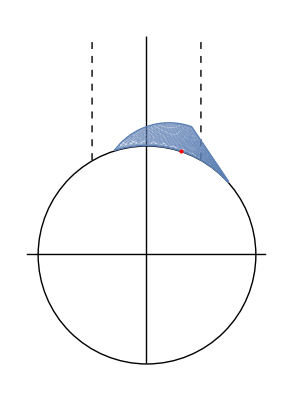

```mathematica
Show[Graphics[Circle[{0,0},1]],
Graphics[Line[{{0,-1},{0,2}}]],
Graphics[Line[{{-1.1,0},{1.1,0}}]],
Graphics[{Dashed,Thick,Line[{{-.5,Sqrt[3]/2},{-.5,2}}]}],
Graphics[{Dashed,Thick,Line[{{.5,Sqrt[3]/2},{.5,2}}]}],
ParametricPlot[{Re[(torusRatio*Exp[I torusAngleFromVectors])],Im[(torusRatio*Exp[I torusAngleFromVectors])]},{α,Pi/2+ArcCos[2 (-1+√2)]/2,Pi},{β,Pi/2+ArcCos[2 (-1+√2)]/2,Pi},RegionFunction->(#4>#3 &&(2 (Sin[#3/2]^2+2 Cos[1/2 (#3+#4-2 ArcCos[2 (-1+Sqrt[2])])] Sin[#3/2] Sin[#4/2]+Sin[#4/2]^2)>1)&)],
(*Least dense globally maximally dense point*)
Graphics[{Red,Point[{Re[(torusRatio*Exp[I torusAngleFromVectors])],Im[(torusRatio*Exp[I torusAngleFromVectors])]}/.{α->2.4907302,β->2.4907302}]}
]]
```

In my world I want this red line to end on the line x=1/2 but it doesn’t....

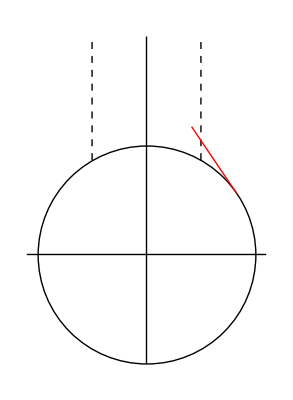

```mathematica
Show[Graphics[Circle[{0,0},1]],
Graphics[Line[{{0,-1},{0,2}}]],
Graphics[Line[{{-1.1,0},{1.1,0}}]],
Graphics[{Dashed,Thick,Line[{{-.5,Sqrt[3]/2},{-.5,2}}]}],
Graphics[{Dashed,Thick,Line[{{.5,Sqrt[3]/2},{.5,2}}]}],
ParametricPlot[{Re[(torusRatio*Exp[I torusAngleFromVectors])],Im[(torusRatio*Exp[I torusAngleFromVectors])]}/.{β->π},{α,Pi/2+ArcCos[2 (-1+√2)]/2,Pi},PlotStyle->{Red,Thick}]
]
```

```mathematica
FullSimplify[{torusRatio*Cos[torusAngle]}/.{β->Pi,α->Pi/2+ArcCos[2 (-1+√2)]/2}]
N[%]
```

{-1+√2}

{0.414214}

```mathematica
FullSimplify[Solve[(torusRatio*Cos[torusAngle]/.β->Pi)==1/2,α]]
N[%]
```

{{α→ConditionalExpression[2 (ArcTan[2/7 √(13+16 √2)]+2 π C[1]),C[1]∈ℤ]},{α→ConditionalExpression[2 (ArcTan[2/7 √(13+16 √2)]+π (-1+2 C[1])),C[1]∈ℤ]}}

{{α→ConditionalExpression[2. (1.04046+6.28319 C[1]),C[1]∈ℤ]},{α→ConditionalExpression[2. (1.04046+3.14159 (-1.+2. C[1])),C[1]∈ℤ]}}

## Density Of Packings

Here we analyze the density of the locally maximally dense packings and explore the density.

```mathematica
torusDensity = FullSimplify[(Pi*(1/2)^2+2*Pi*(1/2(Sqrt[2]-1))^2)/(Norm[latticeVectors[[1]]]*Norm[latticeVectors[[2]]]*Sin[torusAngleFromVectors]) ,{Element[{α,β},Reals],Pi/2+ArcCos[2 (-1+√2)]/2<α<Pi,Pi/2+ArcCos[2 (-1+√2)]/2<β<Pi}]
```

1/8 (-7+4 √2) π Csc[α/2] Csc[β/2] Sec[(α+β)/2+ArcSin[2 (-1+√2)]]

Plot the density over the parameter space

```mathematica
Plot3D[torusDensity,{α,Pi/2+ArcCos[2 (-1+√2)]/2,Pi},{β,Pi/2+ArcCos[2 (-1+√2)]/2,π},RegionFunction->Function[{α,β},α>β],AxesLabel->Automatic]
```

-Graphics3D-

Color the moduli space region with color depending on the density. Red shade is close to 1 and Blue shade is close to .5

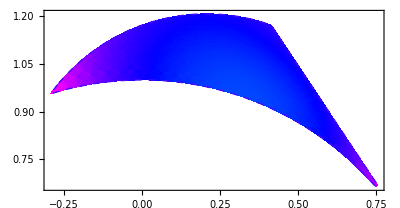

```mathematica
ParametricPlot[{Re[(torusRatio*Exp[I torusAngleFromVectors])],Im[(torusRatio*Exp[I torusAngleFromVectors])]},{α,Pi/2+ArcCos[2 (-1+√2)]/2,Pi},{β,Pi/2+ArcCos[2 (-1+√2)]/2,Pi},RegionFunction->(#4>#3 &&(2 (Sin[#3/2]^2+2 Cos[1/2 (#3+#4-2 ArcCos[2 (-1+Sqrt[2])])] Sin[#3/2] Sin[#4/2]+Sin[#4/2]^2)>1)&),ColorFunction->(Hue[torusDensity]/.{α ->#3,β->#4} &),ColorFunctionScaling->False,BoundaryStyle->Directive[Black,Thick,Dashed],Mesh->None]
```

Now find the minimum density with in the region  (when Pi/2+ArcCos[2 (-1+√2)]/2 < α < π,    Pi/2+ArcCos[2 (-1+√2)]/2 < β < π )

```mathematica
NMinimize[{torusDensity,Pi/2+ArcCos[2 (-1+√2)]/2< α && α < π && Pi/2+ArcCos[2 (-1+√2)]/2< β && β < π &&β>α &&(2 (Sin[α/2]^2+2 Cos[1/2 (α+β-2 ArcCos[2 (-1+Sqrt[2])])] Sin[α/2] Sin[β/2]+Sin[β/2]^2)>1)},{{α,Pi/2+ArcCos[2 (-1+√2)]/2,Pi},{β,Pi/2+ArcCos[2 (-1+√2)]/2,Pi}},AccuracyGoal->20,PrecisionGoal->18,WorkingPrecision->40]
```

{0.6200512143913386472484300436672171760009,{α→2.49073025082147123357055738555461657904,β→2.49073025082147123357055719225403936848}}

```mathematica
NMaximize[{torusDensity,Pi/2+ArcCos[2 (-1+√2)]/2<= α && α <= π && Pi/2+ArcCos[2 (-1+√2)]/2<= β && β <= π && β>=α &&(2 (Sin[α/2]^2+2 Cos[1/2 (α+β-2 ArcCos[2 (-1+Sqrt[2])])] Sin[α/2] Sin[β/2]+Sin[β/2]^2)>=1) },{{α,Pi/2+ArcCos[2 (-1+√2)]/2,Pi},{β,Pi/2+ArcCos[2 (-1+√2)]/2,Pi}},AccuracyGoal->20,PrecisionGoal->18,WorkingPrecision->40]
```

{0.6957360298768663917437082201130257517423,{α→1.868047688116103425184144734768094017441,β→3.141592653589793238462643383279502884197}}

```mathematica
2.4907302508214712335704487708948499642199944162863519875167`40.*180/Pi
```

142.7083312776312420230398681015400308557

```mathematica
N[Sqrt[3]]
```

1.73205

```mathematica
{torusDensity,2 (Sin[α/2]^2+2 Cos[1/2 (α+β-2 ArcCos[2 (-1+Sqrt[2])])] Sin[α/2] Sin[β/2]+Sin[β/2]^2)}/.{β->3.0,α->3.0}
```

{0.789552,1.03043}